```mathematica
Clear[Ne,No];F[θ_]=Sin[θ]^2/Ne^2 +Cos[θ]^2/No^2-π^2/(2 Ne)^2
```

-π^2/(4 Ne^2)+Cos[θ]^2/No^2+Sin[θ]^2/Ne^2

```mathematica
Solve[F[x]==0,x]
```

{{x→ConditionalExpression[ArcTan[-(No √(-4+π^2))/(2 √(Ne^2-No^2)),-(√(4 Ne^2-No^2 π^2))/(√(4 Ne^2-4 No^2))]+2 π C[1],C[1]∈Integers]},{x→ConditionalExpression[ArcTan[-(No √(-4+π^2))/(2 √(Ne^2-No^2)),(√(4 Ne^2-No^2 π^2))/(√(4 Ne^2-4 No^2))]+2 π C[1],C[1]∈Integers]},{x→ConditionalExpression[ArcTan[(No √(-4+π^2))/(2 √(Ne^2-No^2)),-(√(4 Ne^2-No^2 π^2))/(√(4 Ne^2-4 No^2))]+2 π C[1],C[1]∈Integers]},{x→ConditionalExpression[ArcTan[(No √(-4+π^2))/(2 √(Ne^2-No^2)),(√(4 Ne^2-No^2 π^2))/(√(4 Ne^2-4 No^2))]+2 π C[1],C[1]∈Integers]}}

```mathematica
No[λ_]=Sqrt[2.7359+0.01878/(λ^2-0.01822)-0.01354λ^2];
```

```mathematica
Ne[λ_]=Sqrt[2.3753+0.01224/(λ^2-0.01667)-0.01516λ^2];
Ve[λ_]=3*10^11/Ne[λ];Vo[λ_]=3*10^11/No[λ];
```

```mathematica
Vo[0.8]
```

1.80663×10^11

```mathematica
Ve[0.8]
```

1.94248×10^11

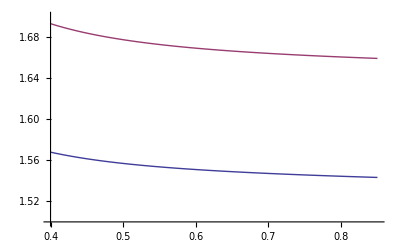

```mathematica
Plot[{Ne[l],No[l]},{l,0.400,0.850},PlotRange->{1.5,1.7}]
```

```mathematica
Clear[L, l1, l2];Time[l1_,l2_,L_]=L*((1/Vo[l1])+(1/Vo[l2])-(1/Ve[l1])-(1/Ve[l2]))- (L/2)*(1/Ve[l1]-1/Vo[l2]);
```

```mathematica
Time[0.404,0.808,1]
```

9.58125×10^-13

```mathematica
Time2[l1_,l2_,L_]=L*((1/Vo[l1])-(1/Ve[l2]));
```

```mathematica
Time2[0.404,0.808,2]
```

9.85826×10^-13

```mathematica
Q[λ_]=ArcTan[-(No[λ] √(-4+π^2))/(2 √(Ne[λ]^2-No[λ]^2))];
```

```mathematica
Q[0.4]
```

1.5708+0.322128 ⅈ

```mathematica
Q[.8]
```

1.5708+0.313143 ⅈ

```mathematica
Q2[λ_]=ArcTan[(√(4 Ne[λ]^2-No[λ]^2 π^2))/(√(4 Ne[λ]^2-4 No[λ]^2))];
```

```mathematica
Q2[0.8]
```

1.28832+0. ⅈ

```mathematica
γ[λ_]=ArcTan[Tan[Q2[λ]](No[λ]/Ne[λ])^2 ]+Q2[λ];
```

```mathematica
γ[0.8]
```

2.61314+0. ⅈ

```mathematica
DL[a_,l_]=l Tan[γ[a]];DL[0.808,2]
```

-1.16756+0. ⅈ

```mathematica
Dϕ[λ_,l_]=(2π l/λ)(No[λ]-(2Ne[λ]/π)(Sqrt[1-Tan[γ[λ]]]));
```

```mathematica
N[Dϕ[0.404,1]]
```

6.70465+0. ⅈ